# Line integral in ℝ^2

## Field

```mathematica
F[{x_, y_}]={-x+y,-x-y};
(*F[{x_, y_}]={1,2}*)
```

## Curve

```mathematica
c[t_]={2Cos[t],2Sin[t]};
```

## Show

```mathematica
a=2;
```

```mathematica
field=VectorPlot[F[{x, y}],{x,-1.2a,1.2a},{y,-1.2a,1.2a},
FrameLabel->{x,y},
VectorPoints->10,
VectorStyle->Arrowheads[0.03]];
```

```mathematica
curve=ParametricPlot[c[t],{t,0,π/2},PlotStyle->{Red,Thickness[0.01]}];
```

```mathematica
xAxis=Graphics[{Text["x",{1.3a,0}],Thickness[0.01],Arrow[{{-1.2a,0},{1.2a,0}}]}];
```

```mathematica
yAxis=Graphics[{Text["y",{0,1.3a}],Thickness[0.01],Arrow[{{0,-1.2a},{0,1.2a}}]}];
```

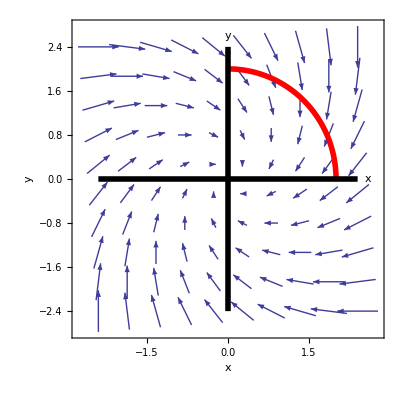

```mathematica
Show[field,curve,xAxis,yAxis]
```

## Integral

```mathematica
NIntegrate[F[c[t]].c'[t],{t,0,π/2}]
```

-6.28319